Similar code is found Jim Swift’s directory
Dropbox/snow/mathematica/coupledCellExamples/Conjecture5.3Code/
This GitHub site has code used for the paper “Anti-synchrony subspaces of weighted networks” by Niholt, Sieben and Swift.

The schematic function, for plotting, is y12: (R^2)^2  -> R^2.  In makes a list of {u1, u2} that produces two plots.
The parameters are ϵ and κ, Greek letters that Mathematica allows us to use.

```mathematica
f[{u_, v_}] := {v, ϵ(1-u^2)v - u}  (* van der pol *)
H = {{0,0},{1,0}};
Ht = Transpose[H];
Clear[x];
x[t_] :={{x11[t],x12[t]}, {x21[t],x22[t]}}
y12[x_] := {x[[1,1]], x[[2,1]]}  (* The schematic function.  This plots u1 and u2 *)

ϵ = 2;
κ = .1;
A = κ{{0,0},{1,1}};
L = κ{{0,0},{-1,1}};
M = L;
printInfo := Module[{},
Print["x' = f[x] + M x H^T, f[u,v] = ", f[{u,v}],", H = ", MatrixForm[H]];
Print["ϵ = " , ϵ,", κ = ", κ,", M = ", κ,MatrixForm[Chop[M/κ]]];
Print["x[0] = ", x0]
]
myPlotStyle ={{Red}, {Blue,  Dashed}};
myPlotRange ={-2.2,2.2};
```

Comment out the SeedRandom[1] command and run the cell to get different initial conditions.

```mathematica
SeedRandom[1];
x0 = RandomReal[{-2, 2}, {2,2}];
```

x' = f[x] + M x H^T, f[u,v] = {v,-u+2 (1-u^2) v}, H = (0 | 0
1 | 0)

ϵ = 2, κ = 0.1, M = 0.1(0 | 0
-1. | 1.)

x[0] = {{1.26956,-1.55432},{1.1581,-1.24879}}

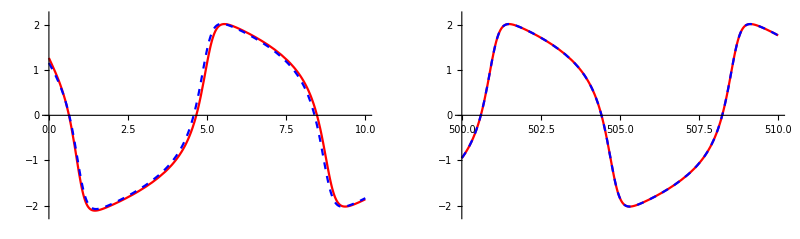

```mathematica
ode = x'[t] ==  Map[f, x[t]]  +  M.x[t].Ht;
ic = x[0] == x0;
ivp = LogicalExpand[ode&& ic];
tPlot = 10;
tTransient = 500;
tMax = tTransient + tPlot;
s = NDSolve[ivp, x[t], {t, 0, tMax}][[1]]; (* s is the first and only solution *)
p1 = Plot[Evaluate[y12[x[t]/.s]], {t, 0, tPlot}, PlotStyle -> myPlotStyle, PlotRange -> myPlotRange];
p2 = Plot[Evaluate[y12[x[t]/.s]], {t, tTransient, tMax}, PlotStyle -> myPlotStyle, PlotRange -> myPlotRange];
printInfo
GraphicsGrid[{{p1, p2}}]
```

Note: The same synchronized solution (with a phase shift) seems to be obtained for all random initial conditions.  The figure was saved with a seed in the random number generator, SeedRandom[1],  so oscillator 1 is always the same.
To save the figures, first use the “Insert file path” menu to point to a directory on your machine

```mathematica
SetDirectory["C:\\Users\\jws8\\Dropbox\\Conjecture5.3\\Article\\Version 1\\"]
(* SetDirectory["/Users/jimswift/Dropbox/Conjecture5.3/Article/Version 1/"] *)
```

C:\Users\jws8\Dropbox\Conjecture5.3\Article\Version 1

```mathematica
If[ϵ == 2 && κ ==  -.1 && M == L, Export["vdpLnegk.pdf", p2, ImageSize -> 300]
];
If[ϵ == 2 && κ == .1 && M == L,Export["vdpLposk.pdf", p2, ImageSize -> 300]
];
If[ϵ == 2 && κ ==  -.1 && M == A, Export["vdpAnegk.pdf", p2, ImageSize -> 300]
];
If[ϵ == 2 && κ == .1 && M == A,Export["vdpAposk.pdf", p2, ImageSize -> 300]
];
```